```mathematica
<<CustomTicks`
```

```mathematica
tickll=LogTicks[-10,10];
Do[tickll[[i,1]]=10^tickll[[i,1]],{i,1,Length[tickll]}];
tickll;
```

#### projections from this work

```mathematica
ma={200,300,500,1000,2000,3000,4000,5000,6000,7000,8000,9000};
(*fa={485,622,858,1156,1133,1219,1137,1078,620,720,491,544};*)
(*mucfa={1823,4917,8754,14306,15567,14827,12590,9269,5881,3021,1167,296};*)
mucfa={257,327,427,640,695,685,620,507,403,292,197,107}/100(*c1=c2=0.01*);
mucvbffa={201,235,303,485,591,618,576,480,388,285,195,107}/100;
mucvbsfa={229,303,396,579,578,521,441,336,246,162,89,33.5}/100;
mucdata=Table[{ma[[i]],mucfa[[i]]},{i,1,Length[ma]}];
mucvbfdata=Table[{ma[[i]],mucvbffa[[i]]},{i,1,Length[ma]}];
mucvbsdata=Table[{ma[[i]],mucvbsfa[[i]]},{i,1,Length[ma]}];
ma3TeV={200,300,500,800,1000,1200,1500,1800,2000,2200,2500,2700,2900};
muc3TeVfa={131,170,188,192,183,170,141,113,94,74,50,31,18}/100(*c1=c2=0.01*);
(*muc3TeVvbffa={110,135,166,177,171,161,135,109,92,73,49,31,18}/100;*)
muc3TeVdata=Table[{ma3TeV[[i]],muc3TeVfa[[i]]},{i,1,Length[ma3TeV]}];
(*muc3TeVvbfdata=Table[{ma3TeV[[i]],muc3TeVvbffa[[i]]},{i,1,Length[ma3TeV]}];*)
```

## MuC projection

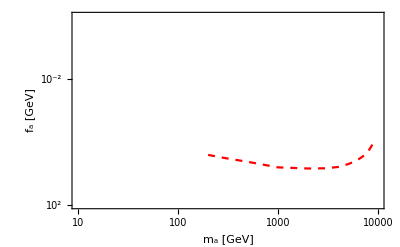

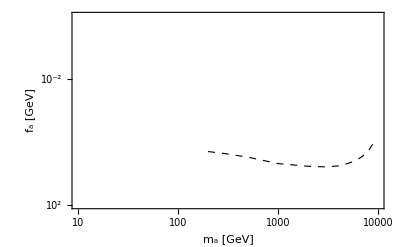

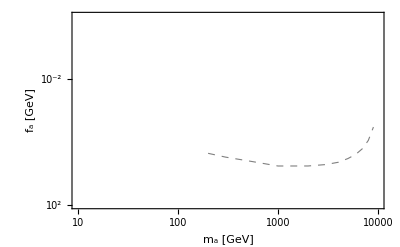

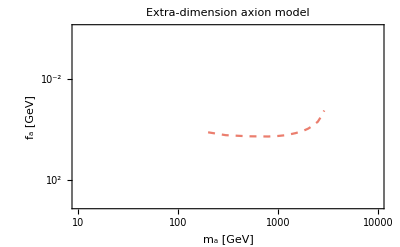

```mathematica
mucplot=ListLogLogPlot[mucdata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-4,10^2}},PlotStyle->{Red,Dashed,Thickness[0.004]},Frame->True,FrameTicks->{{tickll,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a [GeV]",Black,15,FontFamily->"Times"]}(*,PlotLabel->Style["Extra-dimension axion model",Black,18,FontFamily->"Times"]*)]
mucvbfplot=ListLogLogPlot[mucvbfdata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-4,10^2}},PlotStyle->{Black,Dashed,Thickness[0.002]},Frame->True,FrameTicks->{{tickll,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a [GeV]",Black,15,FontFamily->"Times"]}]
mucvbsplot=ListLogLogPlot[mucvbsdata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-4,10^2}},PlotStyle->{Gray,Dashed,Thickness[0.002]},Frame->True,FrameTicks->{{tickll,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a [GeV]",Black,15,FontFamily->"Times"]}]

muc3TeVplot=ListLogLogPlot[muc3TeVdata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-4,10^3}},PlotStyle->{ColorData[24][1],Dashed,Thickness[0.004]},Frame->True,FrameTicks->{{tickll,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a [GeV]",Black,15,FontFamily->"Times"]},PlotLabel->Style["Extra-dimension axion model",Black,18,FontFamily->"Times"]]
(*muc3TeVvbfplot=ListLogLogPlot[muc3TeVvbfdata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-4,10^3}},PlotStyle->{RGBColor[0.574,0.738,0.574,0.8],Dashed,Thickness[0.004]},Frame->True,FrameTicks->{{tickll,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a [GeV]",Black,15,FontFamily->"Times"]},PlotLabel->Style["Extra-dimension axion model",Black,18,FontFamily->"Times"]]*)
```

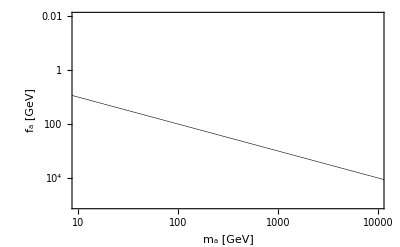

```mathematica
refplot=ListLogLogPlot[{{1,1},{10^5,10^5}},ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-2,10^5}},PlotStyle->{Black,Thickness[0.001]},Frame->True,FrameTicks->{{Automatic,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a [GeV]",Black,15,FontFamily->"Times"]}]
```

## Input data from other experiment constraints

```mathematica
LHCdrellyanold=Import["E:\\李沛然\\课程\\物理\\Particle research\\axion_MuC\\plot\\constraints\\LHC_drellyan.csv","CSV"];
LHCPbPbold=Import["E:\\李沛然\\课程\\物理\\Particle research\\axion_MuC\\plot\\constraints\\LHC_PbPb.csv","CSV"];
LHCggF=Import["E:\\李沛然\\课程\\物理\\Particle research\\axion_MuC\\plot\\constraints\\LHC_ggF.csv","CSV"];
LHC95gammagamma=Import["E:\\李沛然\\课程\\物理\\Particle research\\axion_MuC\\plot\\constraints\\LHC_95GeVdiphoton.csv","CSV"];
LEP=Import["E:\\李沛然\\课程\\物理\\Particle research\\axion_MuC\\plot\\constraints\\LEP.csv","CSV"];
LHClowmassdiphoton=Import["E:\\李沛然\\课程\\物理\\Particle research\\axion_MuC\\plot\\constraints\\LHC_v1_lowmassdiphoton.csv","CSV"];
LHC10to70diphoton=Import["E:\\李沛然\\课程\\物理\\Particle research\\axion_MuC\\plot\\constraints\\LHC_10to70GeV.csv","CSV"];
```

```mathematica
LHCdrellyandata=Table[{LHCdrellyanold[[i]][[1]],1/LHCdrellyanold[[i]][[2]]*Sqrt[2.2*10^-3*10^-4(*c1/c3=0.01*)]/(128*Pi)*1000(*TeV2GeV*)/100(*c1=c2=0.01*)},{i,1,Length[LHCdrellyanold]}];(*photon fusion,require proton in final state*)

LHCPbPbdata=Table[{LHCPbPbold[[i]][[1]],1/LHCPbPbold[[i]][[2]]*Sqrt[2.2*10^-3*10^-4(*c1/c3=0.01*)]/(128*Pi)*1000(*TeV2GeV*)/100(*c1=c2=0.01*)},{i,1,Length[LHCPbPbold]}];
LHCggFdata=Table[{LHCggF[[i]][[1]],1/LHCggF[[i]][[2]]*(0.0168*Sqrt[10^-4(*c1/c3=0.01*)])/(2*Pi)*2(*Subscript[c, γ]=2*)},{i,1,Length[LHCggF]}];
gg2axxs={5.46,5.36,5.14,4.87,4.6,4.38,4.19,4.06,3.93,3.83,3.69,3.59,3.5,3.39,3.32,3.25,3.21,3.16,3.06,3.0,2.95,2.91,2.86,2.83,2.79,2.75,2.72,2.7,2.62,2.6,2.55};(*madgraph generated pp2ax*)
LHC95gammagammadata=Table[{LHC95gammagamma[[i]][[1]],Sqrt[(gg2axxs[[i]]*2.2*10^-3*10^-4(*c1/c3=0.01*))/(LHC95gammagamma[[i]][[2]]*10^-3(*fb2pb*))]*1000},{i,1,Length[LHC95gammagamma]}];
LEPdata=Table[{LEP[[i]][[1]],1/LEP[[i]][[2]]*0.0168/(2*Pi)*2(*Subscript[c, γ]=2*)*Sqrt[2.2*10^-3*10^-4(*c1/c3=0.01*)]/100(*c1=c2=0.01*)},{i,1,Length[LEP]}];
LHClowmassdiphotondata=Table[{LHClowmassdiphoton[[i]][[1]],LHClowmassdiphoton[[i]][[2]]*0.1(*c=10->1*)*(1+1)/(1+5/3)(*Subscript[c, 1]=5/3->1*)*Sqrt[10^-4(*c1/c3=0.01*)]},{i,1,Length[LHClowmassdiphoton]}];
LHC10to70diphotondata=Table[{LHC10to70diphoton[[i]][[1]],LHC10to70diphoton[[i]][[2]]*0.1(*c=10->1*)*1000(*TeVtoGeV*)*1/2(*1/4pi to 1/8pi*)*(1+1)/(1+5/3)(*Subscript[c, 1]=5/3->1*)*Sqrt[10^-4(*c1/c3=0.01*)]},{i,1,Length[LHC10to70diphoton]}];
```

## Plot other experiment constraints

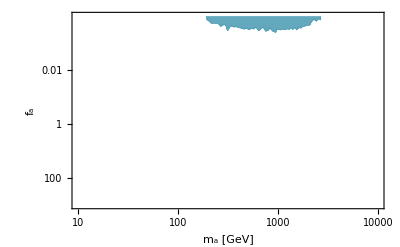

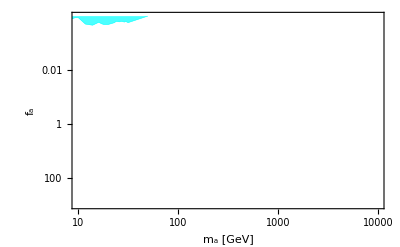

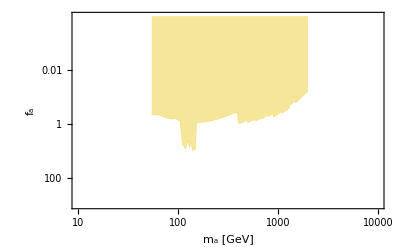

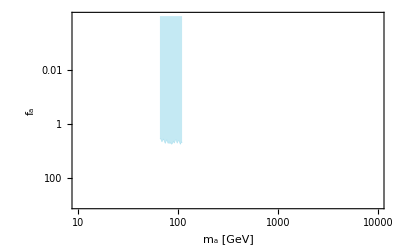

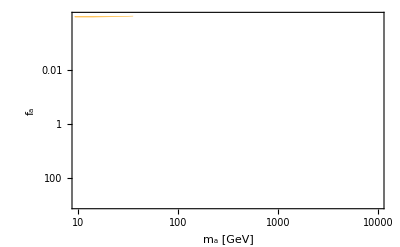

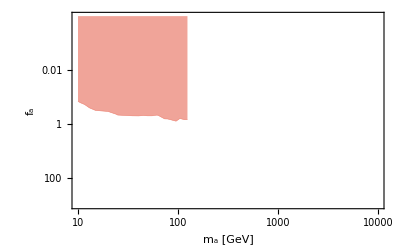

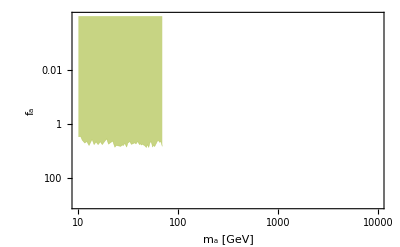

```mathematica
LHCdrellyanplot=ListLogLogPlot[LHCdrellyandata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-4,10^3}},Filling->Top,FillingStyle->Directive[Opacity[0.7],ColorData[24][6]],PlotStyle->{ColorData[24][6],Thickness[0.001]},Frame->True,FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
LHCPbPbplot=ListLogLogPlot[LHCPbPbdata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-4,10^3}},Filling->Top,FillingStyle->Directive[Opacity[0.7],Cyan],PlotStyle->{Cyan,Thickness[0.001]},Frame->True,FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
LHCggFplot=ListLogLogPlot[LHCggFdata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-4,10^3}},Filling->Top,FillingStyle->Directive[Opacity[0.7],ColorData[24][3]],PlotStyle->{ColorData[24][3],Thickness[0.001]},Frame->True,FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
LHC95gammagammaplot=ListLogLogPlot[LHC95gammagammadata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-4,10^3}},Filling->Top,FillingStyle->Directive[Opacity[0.7],ColorData[24][4]],PlotStyle->{ColorData[24][4],Thickness[0.001]},Frame->True,FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
LEPplot=ListLogLogPlot[LEPdata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-4,10^3}},Filling->Top,FillingStyle->Directive[Opacity[0.85],ColorData[24][2]],PlotStyle->{ColorData[24][2],Thickness[0.001]},Frame->True,FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
LHClowmassdiphotonplot=ListLogLogPlot[LHClowmassdiphotondata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-4,10^3}},Filling->Top,FillingStyle->Directive[Opacity[0.7],ColorData[24][1]],PlotStyle->{ColorData[24][1],Thickness[0.001]},Frame->True,FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
LHC10to70diphotonplot=ListLogLogPlot[LHC10to70diphotondata,ScalingFunctions->{Identity,"Reverse"},Joined->True,PlotRange->{{10^1,10^4},{10^-4,10^3}},Filling->Top,FillingStyle->Directive[Opacity[0.7],RGBColor[177/256,196/256,78/256,0.7]],PlotStyle->{RGBColor[177/256,196/256,78/256,0.7],Thickness[0.001]},Frame->True,FrameLabel->{Style["m_a [GeV]",Black,15,FontFamily->"Times"],Style["f_a",Black,15,FontFamily->"Times"]}]
```

## Final Plot

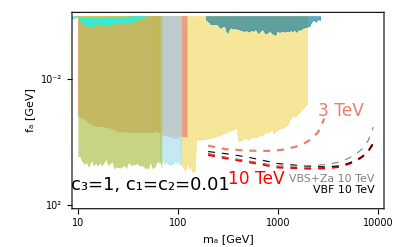

```mathematica
Show[mucplot,mucvbfplot,mucvbsplot,muc3TeVplot(*,muc3TeVvbfplot*),LHCggFplot,LHClowmassdiphotonplot,LHC95gammagammaplot,LHC10to70diphotonplot,LHCPbPbplot,LEPplot,LHCdrellyanplot,Epilog->{Text[Style["c_3=1, c_1=c_2=0.01",Black,18,FontFamily->"Times"],Scaled[{0.25,0.12}],Center,{1,0}],Text[Style["3 TeV",ColorData[24][1],17,FontFamily->"Times"],Scaled[{0.79,0.5}],Left,{1,0}],Text[Style["10 TeV",Red,17,FontFamily->"Times"],Scaled[{0.50,0.15}],Left,{1,0}],Text[Style[Rotate["VBS+Za 10 TeV",0 Degree],Gray,11,FontFamily->"Times"],Scaled[{0.97,0.15}],Right,{1,0}],Text[Style[Rotate["VBF 10 TeV",0 Degree],Black,11,FontFamily->"Times"],Scaled[{0.97,0.095}],Right,{1,0}]}]
```

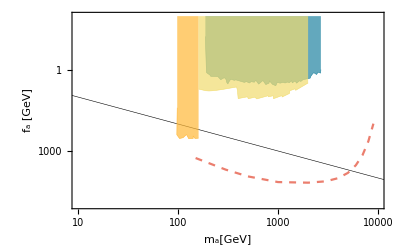

```mathematica
Show[mucplot,refplot,LHCdrellyanplot,LHCdrellyan2plot,LHCH2gammagammaplot]
```